## Matrix forms

```mathematica
Clear[Λ,lhs,rhs,λ,c,G,Λ,lhs,eqn1,eqn2,eqn3,eqn4,eqn5,eqn6,eqn7,eqn8,eqn9];
rep={a[1]->ap, a[-1]->am,b[1]->bp, b[-1]->bm,c[1]->cp, c[-1]->cm,λ[1]->λp, λ[-1]->λm,β[1,1]->βintra,β[-1,-1]->βintra,β[1,-1]->βinter,β[-1,1]->βinter};
(* -Graphics- *)
Λ[χ_,θ_]=τ[χ,θ](λ[χ]-h[χ,θ] + a[χ] Cos[θ]);
(* -Graphics- *)
G[χ_, η_]=1+χ η (Cos[θ] Cos[θp])//TrigExpand;

(* -Graphics- *)
Print["LHS:"];
lhs[χ_,θ_]=Simplify[h[χ,θ]+Λ[χ,θ]/τ[χ,θ]](* = -Graphics-*)
Print["RHS:"];
rhs[χ_,θ_]=β[χ,1]intθf[1,θp] G[χ,1](λ[1]-h[1,θp] + a[1] Cos[θp])+β[χ,-1]intθf[-1,θp]G[χ,-1](λ[-1]-h[-1,θp] + a[-1] Cos[θp])

repl={Cos[θ]->cost,Sin[θ]->sint,Sin[ϕ]->sphi,Cos[ϕ]->cphi};
chi=1;
Print["θ-indep coeff, eq1:"];eqn1=SeriesCoefficient[(lhs[chi,θ]-rhs[chi,θ]/.repl),{cost,0,0}]/.rep//FullSimplify;
Print["Cos[θ] coeff, eq2:"];
eqn2=SeriesCoefficient[(lhs[chi,θ]-rhs[chi,θ]/.repl),{cost,0,1}]/.rep//FullSimplify;

eqn1+ Cos[θ]eqn2==(lhs[chi,θ]-rhs[chi,θ]/.rep)//Simplify

chi=-1;
eqn3=SeriesCoefficient[(lhs[chi,θ]-rhs[chi,θ]/.repl),{cost,0,0}]/.rep//FullSimplify;
eqn4=SeriesCoefficient[(lhs[chi,θ]-rhs[chi,θ]/.repl),{cost,0,1}]/.rep//FullSimplify;
eqn3+ Cos[θ]eqn4==(lhs[chi,θ]-rhs[chi,θ]/.rep)//Simplify

(* Print["charge consvn:"];*)
eqn5=(intθf[1,θp]Λ[1,θp]+intθf[-1,θp]Λ[-1,θp])/.rep//FullSimplify;
```

LHS:

a[χ] Cos[θ]+λ[χ]

RHS:

(1-χ Cos[θ] Cos[θp]) intθf[-1,θp] β[χ,-1] (a[-1] Cos[θp]-h[-1,θp]+λ[-1])+(1+χ Cos[θ] Cos[θp]) intθf[1,θp] β[χ,1] (a[1] Cos[θp]-h[1,θp]+λ[1])

θ-indep coeff, eq1:

Cos[θ] coeff, eq2:

True

True

```mathematica
Clear[arr,array,cmat];arr=CoefficientArrays[{eqn1==0,eqn2==0,eqn3==0,eqn4==0},{λp,ap,λm,am}];
array=Normal[arr]//Simplify;
cmat=array[[2]]//Simplify;
(cmat//MatrixForm)(*/.{intθf[1,θp]->1, intθf[-1,θp]->1}*)
(array[[1]]//MatrixForm)(*/.{intθf[1,θp]->1, intθf[-1,θp]->1}*)
MatrixRank[cmat]
```

(1-βintra intθf[1,θp] | -βintra Cos[θp] intθf[1,θp] | -βinter intθf[-1,θp] | -βinter Cos[θp] intθf[-1,θp]
-βintra Cos[θp] intθf[1,θp] | 1-βintra Cos[θp]^2 intθf[1,θp] | βinter Cos[θp] intθf[-1,θp] | βinter Cos[θp]^2 intθf[-1,θp]
-βinter intθf[1,θp] | -βinter Cos[θp] intθf[1,θp] | 1-βintra intθf[-1,θp] | -βintra Cos[θp] intθf[-1,θp]
βinter Cos[θp] intθf[1,θp] | βinter Cos[θp]^2 intθf[1,θp] | -βintra Cos[θp] intθf[-1,θp] | 1-βintra Cos[θp]^2 intθf[-1,θp])

(βinter h[-1,θp] intθf[-1,θp]+βintra h[1,θp] intθf[1,θp]
Cos[θp] (-βinter h[-1,θp] intθf[-1,θp]+βintra h[1,θp] intθf[1,θp])
βintra h[-1,θp] intθf[-1,θp]+βinter h[1,θp] intθf[1,θp]
Cos[θp] (βintra h[-1,θp] intθf[-1,θp]-βinter h[1,θp] intθf[1,θp]))

4

## solns

```mathematica
FullSimplify[Grad[vf √(kx^2+ky^2+kz^2),{kx,ky,kz}]];
FullSimplify[%.{kx,ky,kz}/.{kx->kf1[θ]Sin[θ] Cos[ϕ],ky->kf1[θ] Sin[θ] Sin[ϕ],kz->kf1[θ] Cos[θ]}]
```

vf √(kf1[θ]^2)

```mathematica
Clear[chi,mvec,Bvec,kf1];
mvec=(-e chi  vf { kx,ky,kz})/(2(kx^2+ky^2+kz^2)) ;
Bvec=B{0,0,1};
Print["omm energy:"];
(*energy corr. from OMM*) dotprod=-mvec.Bvec;
(*energy corr. from OMM*)FullSimplify[dotprod/.{kx->kf1[θ] Sin[θ] Cos[ϕ],ky->kf1[θ] Sin[θ] Sin[ϕ],kz->kf1[θ] Cos[θ]}]
Print["omm velocity:"];
(* vel. from OMM *) FullSimplify[Grad[dotprod,{kx,ky,kz}]];
(* vel. from OMM *) FullSimplify[%/.{kx->kf1[θ] Sin[θ] Cos[ϕ],ky->kf1[θ] Sin[θ] Sin[ϕ],kz->kf1[θ] Cos[θ]}]
```

omm energy:

(B chi e vf Cos[θ])/(2 kf1[θ])

omm velocity:

{-(B chi e vf Cos[θ] Cos[ϕ] Sin[θ])/kf1[θ]^2,-(B chi e vf Cos[θ] Sin[θ] Sin[ϕ])/kf1[θ]^2,-(B chi e vf Cos[2 θ])/(2 kf1[θ]^2)}

```mathematica
Solve[vf kf+(B chi e vf (Cos[θp] Sin[π/2]+Cos[π/2] Cos[ϕp] Sin[θp]))/(2 kf)==μ,kf]//FullSimplify
```

{{kf→(μ-√(μ^2-2 B chi e vf^2 Cos[θp]))/(2 vf)},{kf→(μ+√(μ^2-2 B chi e vf^2 Cos[θp]))/(2 vf)}}

```mathematica
Bvec=B{0,0,1};γ=π/2;mvec1=(-e chi  vf { kx,ky,kz})/(2(kx^2+ky^2+kz^2)) ;
vvec={ Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]}vf//FullSimplify;
Ωvec1=(-chi { Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]})/(2(kf1[θ])^2) ;

(*-Graphics-; -Graphics-; m=-Graphics-;
 in Nandy co's papers, D is defined as inverse of Dphase*)
Print["Phase factor"];
1+e Ωvec1.Bvec

vomm1={-(B chi e vf Cos[θ] Cos[ϕ] Sin[θ])/kf1[θ]^2,-(B chi e vf Cos[θ] Sin[θ] Sin[ϕ])/kf1[θ]^2,-(B chi e vf Cos[2 θ])/(2 kf1[θ]^2)};

Print["v . k :"];
vdotk1= (vf+vomm1.{ Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]})kf1[θ]//FullSimplify
Print["h1:"];
Clear[Dphase1];
(* h1 *)(FullSimplify[ vvec[[3]]+vomm1[[3]]]+FullSimplify[e B Ωvec1. (vvec+vomm1)])/Dphase1[θ]
```

Phase factor

1-(B chi e Cos[θ])/(2 kf1[θ]^2)

v . k :

-(B chi e vf Cos[θ])/(2 kf1[θ])+vf kf1[θ]

h1:

(vf Cos[θ]-(B chi e vf Cos[2 θ])/(2 kf1[θ]^2)+(B chi e vf (B chi e Cos[θ]-2 kf1[θ]^2))/(4 kf1[θ]^4))/Dphase1[θ]

```mathematica
Clear[solve,B,βintra,βinter,γ,vomm1,vomm2,vdotk1,vdotk2,vvec,kf1,mvec1];
solve[B_,βintra_,βinter_]:=Block[{e=1,μ=0.1,vf=0.0005,Bvec,vvec,Ωvec1,mvec1,Ωvec2,mvec2,γ=π/2, η ,θ,ϕ,kf1,kf2,θp,ϕp,chi,Dphase1,Dphase2,vomm1,vomm2,vdotk1,vdotk2,f1,f2,τ1,τ2,h1,h2,zero1,zero2,ct1,ct2,ctct1,ctct2,hzero1,hzero2,hct1,hct2,hstcp1,hstcp2,hstsp1,hstsp2,colvec,mat,sol,Λ1,Λ2,s1,s2},
(* -Graphics- *)
Bvec=B{0,0,1};

chi=1;
(* -Graphics-; -Graphics- *)
kf1[θ_]=(μ+√(μ^2-2 B chi e vf^2 Cos[θ]))/(2 vf);
vvec[θ_]={ Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]}vf;
(*-Graphics-; -Graphics-; m=-Graphics-;
 in Nandy co's papers, D is defined as inverse of Dphase*)
vomm1[θp_]={(B chi e vf (-2 Cos[θp] Cos[ϕp] Sin[γ] Sin[θp]+Cos[γ] (Cos[θp]^2-Cos[2 ϕp] Sin[θp]^2)))/(2 kf1[θp]^2),-((B chi e vf Sin[θp] (Cos[θp] Sin[γ]+Cos[γ] Cos[ϕp] Sin[θp]) Sin[ϕp])/kf1[θp]^2),-((B chi e vf (Cos[2 θp] Sin[γ]+Cos[γ] Cos[ϕp] Sin[2 θp]))/(2 kf1[θp]^2))};

Dphase1[θ_]=1-(2 B chi e vf^2 Cos[θ])/((μ+√(μ^2-2 B chi e vf^2 Cos[θ]))^2);
vdotk1[θ_]=√(μ^2-2 B chi e vf^2 Cos[θ]);
(* -Graphics-from timm-> -Graphics- from review girish*)
h1[θp_]=(vf Cos[θp] (4 μ^4+4 μ^3 √(μ^2-2 B chi e vf^2 Cos[θp])-4 B chi e vf^2 μ Cos[θp] (3 μ+2 √(μ^2-2 B chi e vf^2 Cos[θp]))+B^2 chi^2 e^2 vf^4 (5+3 Cos[2 θp])))/(2 (-2 B chi e vf^2 Cos[θp]+μ (μ+√(μ^2-2 B chi e vf^2 Cos[θp]))) (-B chi e vf^2 Cos[θp]+μ (μ+√(μ^2-2 B chi e vf^2 Cos[θp]))));

(******** second node ***************)
chi=-1;
kf2[θ_]=(μ+√(μ^2-2 B chi e vf^2 Cos[θ]))/(2 vf);
vomm2[θp_]={(B chi e vf^3 Cos[ϕp] Sin[2 θp])/(B chi e vf^2 Cos[θp]-μ (μ+√(μ^2-2 B chi e vf^2 Cos[θp]))),(B chi e vf^3 Sin[2 θp] Sin[ϕp])/(B chi e vf^2 Cos[θp]-μ (μ+√(μ^2-2 B chi e vf^2 Cos[θp]))),(B chi e vf^3 Cos[2 θp])/(B chi e vf^2 Cos[θp]-μ (μ+√(μ^2-2 B chi e vf^2 Cos[θp])))};

Dphase2[θ_]=1-(2 B chi e vf^2 Cos[θ])/((μ+√(μ^2-2 B chi e vf^2 Cos[θ]))^2);
vdotk2[θ_]=√(μ^2-2 B chi e vf^2 Cos[θ]);
h2[θp_]=(vf Cos[θp] (4 μ^4+4 μ^3 √(μ^2-2 B chi e vf^2 Cos[θp])-4 B chi e vf^2 μ Cos[θp] (3 μ+2 √(μ^2-2 B chi e vf^2 Cos[θp]))+B^2 chi^2 e^2 vf^4 (5+3 Cos[2 θp])))/(2 (-2 B chi e vf^2 Cos[θp]+μ (μ+√(μ^2-2 B chi e vf^2 Cos[θp]))) (-B chi e vf^2 Cos[θp]+μ (μ+√(μ^2-2 B chi e vf^2 Cos[θp]))));
(**********************************************************************************************************************************************)
(* -Graphics-; G = 1 + η χ (Cos[θ] Cos[θp]+ Cos[ϕ] Cos[ϕp] Sin[θ] Sin[θp]+Sin[θ] Sin[θp] Sin[ϕ] Sin[ϕp]) *)
τ1[θ_]=(βintra NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp],{θp,0,π}]+
βintra   Cos[θ] NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[θp],{θp,0,π}]+(***** second node  *****)
βinter NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp],{θp,0,π}]-
βinter   Cos[θ] NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp]Cos[θp],{θp,0,π}])^-1;

τ2[θ_]=(βintra NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp],{θp,0,π}]+
βintra   Cos[θ] NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp]Cos[θp],{θp,0,π}]+(***** second node  *****)
βinter NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp],{θp,0,π}]-
βinter   Cos[θ] NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[θp],{θp,0,π}])^-1;


(*-Graphics-*)
f1[θ_]=(Sin[θ] (kf1[θ])^3)/Abs[vdotk1[θ]] Dphase1[θ] τ1[θ];

f2[θ_]=(Sin[θ] (kf2[θ])^3)/Abs[vdotk2[θ]] Dphase2[θ] τ2[θ];
(* Ref. PRB 103,115146 (2021) *)
zero1=Quiet[NIntegrate [f1[θp],{θp,0,π}]];
zero2=Quiet[NIntegrate [f2[θp],{θp,0,π}]];
ct1=Quiet[NIntegrate [f1[θp] Cos[θp],{θp,0,π}]];
ct2=Quiet[NIntegrate [f2[θp] Cos[θp],{θp,0,π}]];
ctct1=Quiet[NIntegrate [f1[θp] Cos[θp]^2,{θp,0,π}]];
ctct2=Quiet[NIntegrate [f2[θp] Cos[θp]^2,{θp,0,π}]];

hzero1=Quiet[NIntegrate [f1[θp] h1[θp],{θp,0,π}]];
hzero2=Quiet[NIntegrate [f2[θp]h2[θp],{θp,0,π}]];
hct1=Quiet[NIntegrate [f1[θp]h1[θp]Cos[θp],{θp,0,π}]];
hct2=Quiet[NIntegrate [f2[θp]h2[θp]Cos[θp],{θp,0,π}]];

colvec=({{βintra hzero1+βinter hzero2}, {βintra hct1-βinter hct2}, {βintra hzero2+βinter hzero1}, {βintra hct2-βinter hct1}});
mat=({{1-βintra zero1, -βintra ct1, -βinter zero2, -βinter ct2}, {-βintra ct1, 1-βintra ctct1, βinter ct2, βinter ctct2}, {-βinter zero1, -βinter ct1, 1-βintra zero2, -βintra ct2}, {βinter ct1, βinter ctct1, -βintra ct2, 1-βintra ctct2}});(* ({{1-βintra intθf[1,θp], -βintra Cos[θp] intθf[1,θp], -βinter intθf[-1,θp], -βinter Cos[θp] intθf[-1,θp]}, {-βintra Cos[θp] intθf[1,θp], 1-βintra Cos[θp]^2 intθf[1,θp], βinter Cos[θp] intθf[-1,θp], βinter Cos[θp]^2 intθf[-1,θp]}, {-βinter intθf[1,θp], -βinter Cos[θp] intθf[1,θp], 1-βintra intθf[-1,θp], -βintra Cos[θp] intθf[-1,θp]}, {βinter Cos[θp] intθf[1,θp], βinter Cos[θp]^2 intθf[1,θp], -βintra Cos[θp] intθf[-1,θp], 1-βintra Cos[θp]^2 intθf[-1,θp]}})*)
sol=LinearSolve[mat,colvec]//Chop;
(* -Graphics- *)
Λ1[θ_]=τ1[θ](sol[[1]]-h1[θ]+sol[[2]] Cos[θ]);
Λ2[θ_]=τ2[θ](sol[[3]]-h2[θ]+sol[[4]] Cos[θ]);
(* PRB 102,205107 (2020) -Graphics-; set γ=0 for Timm's case; (vf χ (-2 k^2+B e χ Cos[θ]))/(4 k^4) *)
s1=NIntegrate[((Sin[θ] (kf1[θ])^3)/Abs[vdotk1[θ]]((vvec[θ]+vomm1[θ])[[3]]+(vf (-2 kf1[θ]^2+B e  Cos[θ]))/(4 kf1[θ]^4)B )Λ1[θ]),{θ,0,π}];
s2=NIntegrate[((Sin[θ] (kf2[θ])^3)/Abs[vdotk2[θ]]((vvec[θ]+vomm2[θ])[[3]]+(-vf (-2 kf2[θ]^2-B e  Cos[θ]))/(4 kf2[θ]^4)B )Λ2[θ]),{θ,0,π}];
{(e B vf^2)/(2 μ^2),s1+s2}
];
solve[100,1,0.5]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.333334,0.000370371,-0.333333,-0.000185186},{0.000370371,0.777778,0.000185186,0.111111},{-0.333333,0.000185186,0.333334,-0.000370371},{-0.000185186,0.111111,-0.000370371,0.777778}} may contain significant numerical errors.

{0.00125,-9.7222×10^-8}

{{0.0000125,-3.24074×10^-8},{0.000025,-3.24074×10^-8},{0.0000375,-3.24074×10^-8},{0.00005,-3.24074×10^-8},{0.0000625,-3.24074×10^-8},{0.000075,-3.24074×10^-8},{0.0000875,-3.24074×10^-8},{0.0001,-3.24074×10^-8},{0.0001125,-3.24074×10^-8},{0.000125,-3.24074×10^-8}}

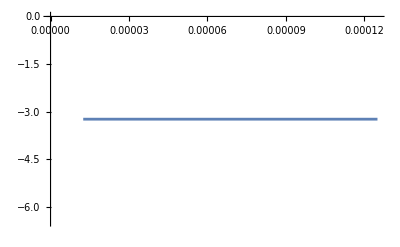

```mathematica
vintra=3;vinter=vintra/2;
dat1=Table[Quiet[solve[B,vintra,vinter]],{B,1,10,1}]
list=dat1;
len=Length[list];
scale=10^8(*list[[1,2]]*);
dat=Table[{list[[i,1]],list[[i,2]] scale},{i,1,len}];
ListLinePlot[{dat}]
```

## not in linearsolve way

```mathematica
Clear[solve,B,βintra,βinter,γ,vomm1,vomm2,vdotk1,vdotk2,vvec,kf1,mvec1];

sig[B_,βintra_,βinter_]:=Block[{e=1,μ=0.1,vf=0.005,Bvec,vvec,Ωvec1,mvec1,Ωvec2,mvec2,γ=π/2, η ,θ,ϕ,kf1,kf2,θp,ϕp,chi,Dphase1,Dphase2,vomm1,vomm2,vdotk1,vdotk2,f1,f2,τ1,τ2,h1,h2,zero1,zero2,ct1,ct2,ctct1,ctct2,hzero1,hzero2,hct1,hct2,hstcp1,hstcp2,hstsp1,hstsp2,colvec,mat,sol,Λ1,Λ2,s1,s2,λ1,a1,λ2,a2,int1,int2,eq5,matr},
(* -Graphics- *)
Bvec=B{0,0,1};

chi=1;
(* -Graphics-; -Graphics- *)
kf1[θ_]=(μ+√(μ^2-2 B chi e vf^2 Cos[θ]))/(2 vf);
vvec[θ_]={ Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]}vf;
(*-Graphics-; -Graphics-; m=-Graphics-;
 in Nandy co's papers, D is defined as inverse of Dphase*)
vomm1[θ_]={-(B chi e vf Cos[θ] Cos[ϕ] Sin[θ])/kf1[θ]^2,-(B chi e vf Cos[θ] Sin[θ] Sin[ϕ])/kf1[θ]^2,-(B chi e vf Cos[2 θ])/(2 kf1[θ]^2)};

Dphase1[θ_]=1-(B chi e Cos[θ])/(2 kf1[θ]^2);
vdotk1[θ_]=vf kf1[θ] -(B e vf chi Cos[θ])/(2 kf1[θ]);
(* -Graphics-from timm-> -Graphics- from review girish*)
h1[θp_]=1/Dphase1[θp](vf Cos[θp]-(B chi e vf Cos[2 θp])/(2 kf1[θp]^2)+(B chi e vf (B chi e Cos[θp]-2 kf1[θp]^2))/(4 kf1[θp]^4));

(******** second node ***************)
chi=-1;
kf2[θ_]=(μ+√(μ^2-2 B chi e vf^2 Cos[θ]))/(2 vf);
vomm2[θ_]={-(B chi e vf Cos[θ] Cos[ϕ] Sin[θ])/kf2[θ]^2,-(B chi e vf Cos[θ] Sin[θ] Sin[ϕ])/kf2[θ]^2,-(B chi e vf Cos[2 θ])/(2 kf2[θ]^2)};

Dphase2[θ_]=1-(B chi e Cos[θ])/(2 kf2[θ]^2);
vdotk2[θ_]=vf kf2[θ]-(B e vf chi Cos[θ])/(2 kf2[θ]);
h2[θp_]=1/Dphase2[θp](vf Cos[θp]-(B chi e vf Cos[2 θp])/(2 kf2[θp]^2)+(B chi e vf (B chi e Cos[θp]-2 kf2[θp]^2))/(4 kf2[θp]^4));
(**********************************************************************************************************************************************)
(* -Graphics-; G = 1 + η χ (Cos[θ] Cos[θp]+ Cos[ϕ] Cos[ϕp] Sin[θ] Sin[θp]+Sin[θ] Sin[θp] Sin[ϕ] Sin[ϕp]) *)
τ1[θ_]=(βintra NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp],{θp,0,π}]+
βintra   Cos[θ] NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[θp],{θp,0,π}]+
(***** second node  *****)
βinter NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp],{θp,0,π}]-
βinter   Cos[θ] NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp]Cos[θp],{θp,0,π}])^-1;

τ2[θ_]=(βintra NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp],{θp,0,π}]+
βintra   Cos[θ] NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp]Cos[θp],{θp,0,π}]+
(***** second node  *****)
βinter NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp],{θp,0,π}]-
βinter   Cos[θ] NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[θp],{θp,0,π}])^-1;


(*-Graphics-*)
f1[θ_]=(Sin[θ] (kf1[θ])^3)/Abs[vdotk1[θ]] Dphase1[θ] τ1[θ];

f2[θ_]=(Sin[θ] (kf2[θ])^3)/Abs[vdotk2[θ]] Dphase2[θ] τ2[θ];
(* Ref. PRB 103,115146 (2021) *)
zero1=Quiet[NIntegrate [f1[θp],{θp,0,π}]];
zero2=Quiet[NIntegrate [f2[θp],{θp,0,π}]];
ct1=Quiet[NIntegrate [f1[θp] Cos[θp],{θp,0,π}]];
ct2=Quiet[NIntegrate [f2[θp] Cos[θp],{θp,0,π}]];
ctct1=Quiet[NIntegrate [f1[θp] Cos[θp]^2,{θp,0,π}]];
ctct2=Quiet[NIntegrate [f2[θp] Cos[θp]^2,{θp,0,π}]];

hzero1=Quiet[NIntegrate [f1[θp] h1[θp],{θp,0,π}]];
hzero2=Quiet[NIntegrate [f2[θp]h2[θp],{θp,0,π}]];
hct1=Quiet[NIntegrate [f1[θp]h1[θp]Cos[θp],{θp,0,π}]];
hct2=Quiet[NIntegrate [f2[θp]h2[θp]Cos[θp],{θp,0,π}]];

colvec=({{βintra hzero1+βinter hzero2}, {βintra hct1-βinter hct2}, {βintra hzero2+βinter hzero1}, {βintra hct2-βinter hct1}});
matr=({{1-βintra zero1, -βintra ct1, -βinter zero2, -βinter ct2}, {-βintra ct1, 1-βintra ctct1, βinter ct2, βinter ctct2}, {-βinter zero1, -βinter ct1, 1-βintra zero2, -βintra ct2}, {βinter ct1, βinter ctct1, -βintra ct2, 1-βintra ctct2}});
mat=matr.({{λ1}, {a1}, {λ2}, {a2}});
(* ({{1-βintra intθf[1,θp], -βintra Cos[θp] intθf[1,θp], -βinter intθf[-1,θp], -βinter Cos[θp] intθf[-1,θp]}, {-βintra Cos[θp] intθf[1,θp], 1-βintra Cos[θp]^2 intθf[1,θp], βinter Cos[θp] intθf[-1,θp], βinter Cos[θp]^2 intθf[-1,θp]}, {-βinter intθf[1,θp], -βinter Cos[θp] intθf[1,θp], 1-βintra intθf[-1,θp], -βintra Cos[θp] intθf[-1,θp]}, {βinter Cos[θp] intθf[1,θp], βinter Cos[θp]^2 intθf[1,θp], -βintra Cos[θp] intθf[-1,θp], 1-βintra Cos[θp]^2 intθf[-1,θp]}}) *)


eq5=λ2 zero2+a2 ct2-hzero2+λ1 zero1 + a1 ct1-hzero1;

sol=Flatten[Solve[{mat[[1]]+colvec[[1]]==0,mat[[2]]+colvec[[2]]==0,mat[[3]]+colvec[[3]]==0,mat[[4]]+colvec[[4]]==0,eq5==0},{λ1,a1,λ2,a2}],1];

Λ1[θ_]=τ1[θ](λ1-h1[θ] + a1 Cos[θ])/.sol;    Λ2[θ_]=τ2[θ](λ2-h2[θ] + a2 Cos[θ])/.sol;
int1[θ_]=(Sin[θ] (kf1[θ])^3)/Abs[vdotk1[θ]](vf Cos[θ]-(B  e vf Cos[2 θ])/(2 kf1[θ]^2)+(vf (-2 kf1[θ]^2+B e  Cos[θ]))/(4 kf1[θ]^4)B )Λ1[θ];
int2[θ_]=(Sin[θ] (kf2[θ])^3)/Abs[vdotk2[θ]](vf Cos[θ]+(B  e vf Cos[2 θ])/(2 kf2[θ]^2)+(-vf (-2 kf2[θ]^2-B e  Cos[θ]))/(4 kf2[θ]^4)B )Λ2[θ];
s1=NIntegrate[int1[θ],{θ,0,π}];
s2=NIntegrate[int2[θ],{θ,0,π}];
{(e B vf^2)/(2 μ^2),s1+s2,matr//MatrixForm,MatrixRank[matr],sol}
];
sig[11,1,0.5]
```

{0.01375,-0.0000125013,(0.333371 | 0.0040751 | -0.333315 | -0.00203755
0.0040751 | 0.777811 | 0.00203755 | 0.111094
-0.333315 | 0.00203755 | 0.333371 | -0.0040751
-0.00203755 | 0.111094 | -0.0040751 | 0.777811),3,{λ1→0.0000286474,a1→-0.000624959,λ2→-0.0000286474,a2→-0.000624959}}

{{0.000125,-4.16667×10^-6},{0.001375,-4.16667×10^-6},{0.002625,-4.16668×10^-6},{0.003875,-4.1667×10^-6},{0.005125,-4.16673×10^-6},{0.006375,-4.16676×10^-6},{0.007625,-4.1668×10^-6},{0.008875,-4.16685×10^-6},{0.010125,-4.16691×10^-6},{0.011375,-4.16697×10^-6}}

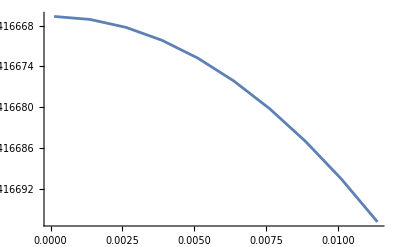

```mathematica
vintra=3;vinter=vintra/2;
dat1=Table[Quiet[sig[B,vintra,vinter]],{B,0.1,10,1}]
list=dat1;
len=Length[list];
scale=1(*list[[1,2]]*);
dat=Table[{list[[i,1]],list[[i,2]] scale},{i,1,len}];
ListLinePlot[{dat}]
```

```mathematica
0.000038==3.8 ×10^-5
```

True